```mathematica
r1[t_] = {L/2 Sin[q1[t]], -L/2 Cos[q1[t]],0};
v1[t_] = D[r1[t],t];
r2[t_] = {L Sin[q1[t]]+L/2 Sin[q2[t]], -L Cos[q1[t]]-L/2  Cos[q2[t]],0};
v2[t_]= D[r2[t],t];
T[t_]= Simplify[1/2m (Dot[v1[t],v1[t]]+Dot[v2[t],v2[t]])+1/24m  L^2 (q1'[t]^2+q2'[t]^2)]
V[t_] = -m g 3L/2 Cos[q1[t]]-m g L/2 Cos[q2[t]]
LL[t_] = T[t] - V[t];
Simplify[D[LL[t],q1[t]]]
A1[t_] = Simplify[D[LL[t],q1'[t]]]
Simplify[A1'[t]]
Simplify[D[LL[t],q2[t]]]
A2[t_] = Simplify[D[LL[t],q2'[t]]]
Simplify[A2'[t]]
Simplify[Simplify[D[A1[t],t]]== Simplify[D[LL[t],q1[t]]]]
Simplify[Simplify[D[A2[t],t]]== Simplify[D[LL[t],q2[t]]]]
```

1/6 L^2 m (4 q1'[t]^2+3 Cos[q1[t]-q2[t]] q1'[t] q2'[t]+q2'[t]^2)

-3/2 g L m Cos[q1[t]]-1/2 g L m Cos[q2[t]]

-1/2 L m (3 g Sin[q1[t]]+L Sin[q1[t]-q2[t]] q1'[t] q2'[t])

1/6 L^2 m (8 q1'[t]+3 Cos[q1[t]-q2[t]] q2'[t])

1/6 L^2 m (-3 Sin[q1[t]-q2[t]] (q1'[t]-q2'[t]) q2'[t]+8 q1''[t]+3 Cos[q1[t]-q2[t]] q2''[t])

1/2 L m (-g Sin[q2[t]]+L Sin[q1[t]-q2[t]] q1'[t] q2'[t])

1/6 L^2 m (3 Cos[q1[t]-q2[t]] q1'[t]+2 q2'[t])

1/6 L^2 m (-3 Sin[q1[t]-q2[t]] q1'[t] (q1'[t]-q2'[t])+3 Cos[q1[t]-q2[t]] q1''[t]+2 q2''[t])

L m (9 g Sin[q1[t]]+3 L Sin[q1[t]-q2[t]] q2'[t]^2+8 L q1''[t]+3 L Cos[q1[t]-q2[t]] q2''[t])==0

L m (3 g Sin[q2[t]]-3 L Sin[q1[t]-q2[t]] q1'[t]^2+3 L Cos[q1[t]-q2[t]] q1''[t]+2 L q2''[t])==0

```mathematica
I1o = 1/12 m L^2 +L^2/4 m;
I2c = 1/12 m L^2;
FG1 ={0,-m g,0};
FG2 ={0,-m g,0};
F =Simplify[ m r2''[t]-FG2]
rp[t] = 2 *r1[t];
Simplify[rp[t]-r2[t]]
eqns = {I1o q1''[t]== Simplify[Cross[r1[t],FG1][[3]]+Cross[rp[t],-F][[3]]],I2c q2''[t]== Simplify[Cross[rp[t]-r2[t],F][[3]]] }
Simplify[I1o q1''[t]== Simplify[Cross[r1[t],FG1][[3]]+Cross[rp[t],-F][[3]]]]
Simplify[I2c q2''[t]== Cross[rp[t]-r2[t],F][[3]]]
(*r[t_] = Simplify[1/2(r1[t]+r2[t])]
theta[t_] = VectorAngle[r[t],{0,-1,0}]
Io = 2/12 m L^2 +m (Norm[r1[t]-r2[t]]^2 + Norm[r[t]]^2)
FG = {0,-2m g,0};*)
```

{-1/2 L m (2 Sin[q1[t]] q1'[t]^2+Sin[q2[t]] q2'[t]^2-2 Cos[q1[t]] q1''[t]-Cos[q2[t]] q2''[t]),m (g+L Cos[q1[t]] q1'[t]^2+1/2 L Cos[q2[t]] q2'[t]^2+L Sin[q1[t]] q1''[t]+1/2 L Sin[q2[t]] q2''[t]),0}

{-1/2 L Sin[q2[t]],1/2 L Cos[q2[t]],0}

{1/3 L^2 m q1''[t]==-1/2 L m (3 g Sin[q1[t]]+L Sin[q1[t]-q2[t]] q2'[t]^2+2 L q1''[t]+L Cos[q1[t]-q2[t]] q2''[t]),1/12 L^2 m q2''[t]==-1/4 L m (2 g Sin[q2[t]]-2 L Sin[q1[t]-q2[t]] q1'[t]^2+2 L Cos[q1[t]-q2[t]] q1''[t]+L q2''[t])}

L m (9 g Sin[q1[t]]+3 L Sin[q1[t]-q2[t]] q2'[t]^2+8 L q1''[t]+3 L Cos[q1[t]-q2[t]] q2''[t])==0

L m (3 g Sin[q2[t]]-3 L Sin[q1[t]-q2[t]] q1'[t]^2+3 L Cos[q1[t]-q2[t]] q1''[t]+2 L q2''[t])==0

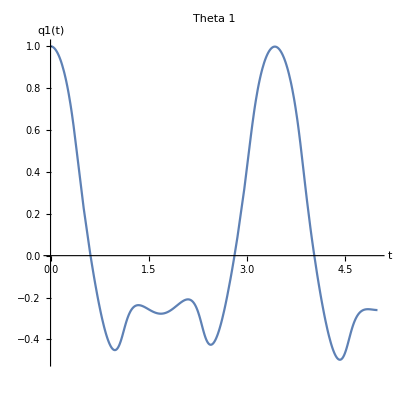

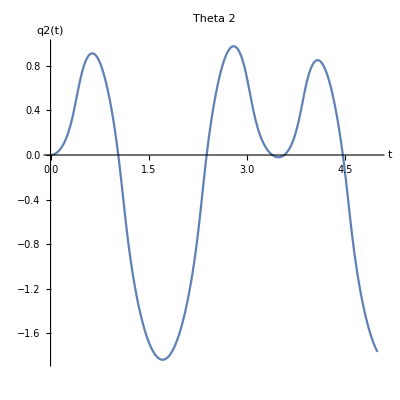

-Graphics-

-Graphics-

```mathematica
m=10;
L=2;
g=9.8;
tf = 5;
sol1 = NDSolve[{Simplify[D[A1[t],t]]== Simplify[D[LL[t],q1[t]]],Simplify[D[A2[t],t]]== Simplify[D[LL[t],q2[t]]],q1[0]==1,q2[0]==0,q1'[0]== 0,q2'[0]==0},{q1[t],q2[t]},{t,0,tf}];
sol2 = NDSolve[{eqns,q1[0]==1,q2[0]==0,q1'[0]== 0,q2'[0]==0},{q1[t],q2[t]},{t,0,tf}];
Plot[sol1[[1,1,2]],{t,0,tf},PlotLabel->"Theta 1",AxesLabel->{"t","q1(t)"},AspectRatio->1]
Plot[sol1[[1,2,2]],{t,0,tf},PlotLabel->"Theta 2",AxesLabel->{"t","q2(t)"},AspectRatio->1]
Plot[sol2[[1,1,2]],{t,0,tf},PlotLabel->"Theta 1",AxesLabel->{"t","q1(t)"},AspectRatio->1]
Plot[sol2[[1,2,2]],{t,0,tf},PlotLabel->"Theta 2",AxesLabel->{"t","q2(t)"},AspectRatio->1]
```